"Стар

(3, 2)

(10, 2)

(10, 15)

(5, 15)

(5, 13)

(3, 13)

4!  =  24

Всего жителей: 2008715

Количество абонентов, имеющих удовлетворительное качество связи: 917240

Карта мощности сигнала

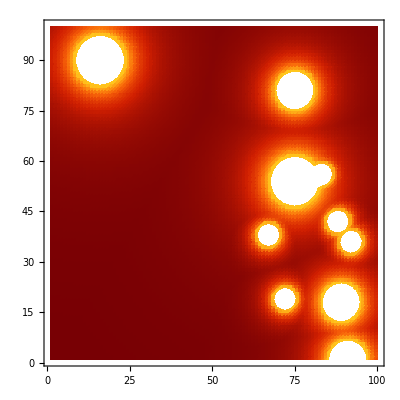

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

По часовой стрелке

Старт

(10, 2)

(3, 2)

(3, 13)

(5, 13)

(5, 15)

(10, 15)

(10, 2)

Конец

```mathematica
(*Реализация подсчета факториал через рекурсивную процедуру*)
Factorial1[n_]:=If[n==0,1,If[n<0,Print["Факториал отрицательного числа не существует"],n*Factorial1[n-1]]]
(*Factorial1[5]*)
n=4;
Print[n,("!  =  "),Factorial1[n]];

power=Table[0,{100},{100}];      (*Матрица Мощности Сигнала*)
powerflag=Table[0,{100},{100}];         (*матрица вышек*)
population=Table[0,{100},{100}];     (*Матрица Плотности Населения*)
amount=0;
For[i=1,i<=100,i++,                                                      (*распределение населения*)
For[j=1,j<=100,j++,
population[[i,j]]=RandomInteger[{0,400}];
amount+=population[[i,j]];
]]

p1=100;
p2=300;
p3=500;
n1=5;
n2=3;
n3=2;

Razm[n_,power_, powerflag_,p_]:=Module[{mas=power,masflag=powerflag},                  (*функция для размещения вышек*)
For[j=1,j≤n,j++,
While[True,                      (*проверка на повторение*)
a=RandomInteger[{1,100}];
b=RandomInteger[{1,100}];
If[masflag[[a,b]]≠1,
masflag[[a,b]]=1;
Break[]]
];
mas[[a,b]]=p;
For[i=1,i≤100,i++,                          (*сразу расчитываем мощность для всех областей в зависимости от вышки и расстояния*)
For[q=1,q≤100,q++,
If[i≠a||q≠b,
pnew=p/((a-i)^2+(b-q)^2);
If[pnew>mas[[i,q]],mas[[i,q]]=pnew]]]]];
Return [mas]]
power=Razm[n1,power,powerflag,p1];
power=Razm[n2,power,powerflag,p2];
power=Razm[n3,power,powerflag,p3];

amountofgood=0;                      (*подсчет пользователей с хорошим сигналаом*)
For[i=1,i<=100,i++,
For[j=1,j<=100,j++,
If[power[[i,j]]>1,amountofgood+=population[[i,j]]]
]]

Print["Всего жителей: ", amount];
Print["Количество абонентов, имеющих удовлетворительное качество связи: ",amountofgood];
Print["Карта мощности сигнала"];
ListDensityPlot[power, ColorFunction->"SolarColors"]

mas=Table[0,{15},{15}];
mas[[3,2]]=1;
mas[[3,13]]=1;
mas[[5,13]]=1;
mas[[5,15]]=1;
mas[[10,15]]=1;
mas[[10,2]]=1;
Print[MatrixForm[mas]];

flag=0;
While[flag≠1,             (*наугад выбираем стартовую точку*)
a=RandomInteger[{1,15}];
For[j=1,j<15,j++,
If[mas[[a,j]]==1,
b=j;
flag=1;
Break[]]]
]
abeg=a;
bbeg=b;
predi=a;
predj=b;

flag1=RandomInteger[{1,0}];
If[flag1==1,Print["По часовой стрелке"],Print["Против часовой стрелки"]]
Print["Старт"];
Print["(",a,", ", b,")"]; 
While[True,                       (*поиск всех оставшихся точек покругу*)
flag=0;
For[j=b-1,j>=1,j--,                                  (*проверка влево*)
If[mas[[a,j]]==1 &&j!=predj, 
Print["(",a,", ", j,")"]; 
predj=b;
b=j;
flag=1;
Break[]]]
If[flag1==1,
If[flag≠1,                                           (*проверка вверх*)
For[i=a-1,i>=1,i--, 
If[i==predi&&b==predj,Break[]];
If[mas[[i,b]]==1 &&i!=predi , 
Print["(",i,", ", b,")"];
predi=a;
a=i;
flag=1;
Break[]]]]

If[flag≠1 ,                                           (*проверка вправо*)
For[j=b+1,j≤15,j++,
If[mas[[a,j]]==1&&j!=predj, 
Print["(",a,", ", j,")"]; 
predj=b;
b=j;
flag=1;
Break[]]]]

If[flag≠1,                                           (*проверка вниз*)
For[i=a+1,i<=15,i++, 
If[mas[[i,b]]==1&&i!=predi, 
Print["(",i,", ", b,")"];
predi=a;
a=i;
flag=1;
Break[]]]],
If[flag≠1,                                           (*проверка вниз*)
For[i=a+1,i<=15,i++, 
If[mas[[i,b]]==1&&i!=predi, 
Print["(",i,", ", b,")"];
predi=a;
a=i;
flag=1;
Break[]]]]
If[flag≠1,                                           (*проверка вверх*)
For[i=a-1,i>=1,i--, 
If[i==predi&&b==predj,Break[]];
If[mas[[i,b]]==1 &&i!=predi , 
Print["(",i,", ", b,")"];
predi=a;
a=i;
flag=1;
Break[]]]]
If[flag≠1 ,                                           (*проверка вправо*)
For[j=b+1,j≤15,j++,
If[mas[[a,j]]==1&&j!=predj, 
Print["(",a,", ", j,")"]; 
predj=b;
b=j;
flag=1;
Break[]]]]
]
If[abeg==a&&bbeg==b,Break[]];
]

Print["Конец"];
```